```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
n = 5;
data = RandomVariate[PoissonDistribution[11],{n}]
```

{17,6,11,13,16}

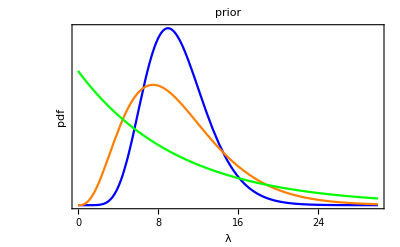

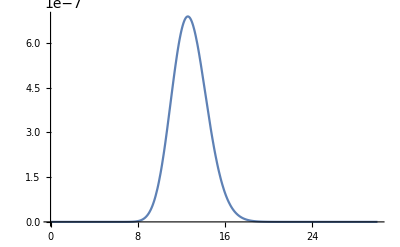

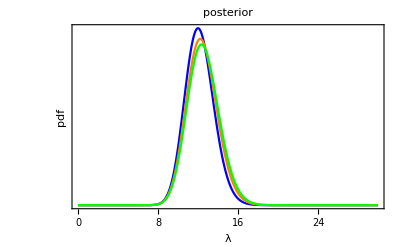

```mathematica
α1=10;
β1 = 1;
α2=4;
β2 = 2.5;
α3 = 1;
β3 = 10;
gPrior=Plot[{PDF[GammaDistribution[α1,β1],x],PDF[GammaDistribution[α2,β2],x],PDF[GammaDistribution[α3,β3],x]},{x,0,30},PlotLabel->"prior",PlotRange->Full,Frame->{True,True,False,False},PlotStyle->{Blue,Orange,Green},FrameTicks->{True,False},FrameLabel->{"λ","pdf"},BaseStyle->{FontSize->16}]
gLikelihood = Plot[Likelihood[PoissonDistribution[λ],data],{λ,0,30},PlotRange->Full]
gPosterior = Plot[{PDF[GammaDistribution[α1+Total@data,β1/(n β1+1)],x],PDF[GammaDistribution[α2+Total@data,β2/(n β2+1)],x],PDF[GammaDistribution[α3+Total@data,β3/(n β3+1)],x]},{x,0,30},PlotRange->Full,PlotLabel->"posterior",Frame->{True,True,False,False},PlotStyle->{Blue,Orange,Green},FrameTicks->{True,False},FrameLabel->{"λ","pdf"},BaseStyle->{FontSize->16}]
```

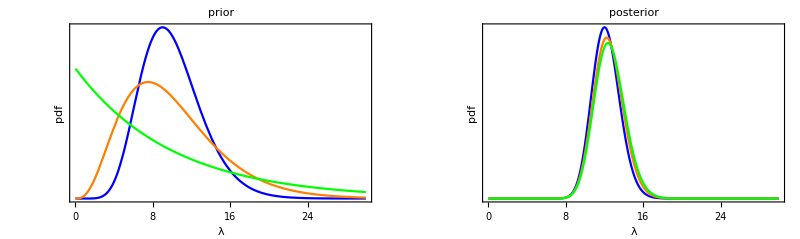

```mathematica
gFinal=Show[GraphicsRow[{gPrior,gPosterior}],ImageSize->800]
```

```mathematica
Export["Distributions_gammaPrior.pdf",gFinal]
```

Distributions_gammaPrior.pdf